Sailing is a very complex sport deeply based in physics also requiring a lot of tactics to analyze the best path to get around the course in a race. In my project, I created a wind tunnel with the Lattice Boltzmann method to analyze how much lift  will be generated for different combinations of wind speed, boat angle and sail angle. I then applied the results to a generated wind vector field to optimize the path between one point and another.

## Introduction

Sailing straight into the wind is obviously impossible, so in order to sail upwind, I must sail at around 45 degree angles off the wind direction to slowly zigzag my way up the course. By heading a lower angle (larger angle from the wind direction), the boat will increase in speed but increase in distance sailed, and in sailing one of the challenges is to be able to constantly find the perfect balance between speed and distance to sail. Another integral part of sailing is to analyze the wind and look for gusts (patches of stronger wind) and shifts (wind direction changes). In order to sail around the course quickly, I must sail to the gusts as soon as possible as well as choose the correct side to sail to: right when the wind shifts right and left when the wind shifts left.

## Designing the sails

I used two manipulate functions and Bezier curves to manually adjust the sail-shape while making sure the arc-length stays constant and accurate to the real life measurements.

### Making the jib

The jib is the smaller of the two sails and is positioned in front of the mainsail to redirect the flow of wind into the mainsail, therefore the jib has an open leach so air can flow out of the jib into the main sail.

The arc length of the jib should be roughly 169 cm and the difference between the x value of the two endpoints should be 163 cm.

jmat is the rotation matrix for the jib

jpts are the points used for the bezier curve

ja is the manipulated variable to adjust the depth of the sail near the front

jb is the manipulated variable for how open the sail is at the back

jAOA is the angle the jib will be facing in relation to the boat angle

I chose 37.5 for ja and 30 for jb.

```mathematica
Clear[jmat,jpts,ja,jb,jt,jAOA];
Manipulate[jpts={{0,0},{50,ja},{163,jb}};
jmat={{Cos[(jAOA) Degree],-Sin[(jAOA) Degree]},{Sin[(jAOA) Degree],Cos[(jAOA) Degree]}};
jf=BezierFunction[jpts];
ParametricPlot[jmat.{jf[jt][[1]],jf[jt][[2]]},{jt,0,1},AspectRatio->Automatic,ImageSize->Medium,PlotRange->{{0,200},{-45,40}}],{{ja,0.9},0.1,50},{{jb,0.9},0.1,50},{{jAOA,0,"Angle of Attack"},-45,45},Dynamic[StringJoin["Arc length: ",ToString[NIntegrate[Sqrt[Power[D[2(1−jt)jt*50+(jt^2)*163,jt],2]+Power[D[2(1−jt)jt*ja+(jt^2)*jb,jt],2]],{jt,0,1}]]," cm"]],SaveDefinitions->True]
```

### Making the mainsail

The mainsail is much larger than the jib but has a closed leach in order to provide more lift.

The arc length of the main should be approximately 199.5 cm and the distance between the two endpoints should be 194 cm .

mat is the rotation matrix for the main sail

pts are the points used for the bezier curve

a is the manipulated variable to adjust the depth of the sail near the front

b is the manipulated variable to adjust the depth of the sail near the back

AOA is the angle the main sail will be facing in relation to the boat angle

I chose 20 for a and 30 for b.

```mathematica
Clear[mat,pts,a,b,t,AOA];
Manipulate[pts={{0,0},{50,a},{150,b},{194,0}};
mat={{Cos[(AOA) Degree],-Sin[(AOA) Degree]},{Sin[(AOA) Degree],Cos[(AOA) Degree]}};
f=BezierFunction[pts];
ParametricPlot[mat.{f[t][[1]],f[t][[2]]},{t,0,1},AspectRatio->Automatic,ImageSize->Medium,PlotRange->{{0,250},{-35,30}}],{{a,0.9},0.1,50},{{b,0.9},0.1,50},{{AOA,0,"Angle of Attack"},-45,45},Dynamic[StringJoin["Arc length: ",ToString[NIntegrate[Sqrt[Power[D[3((1−t)^2)t*50+3(1−t)(t^2)150+(t^3)*194,t],2]+Power[D[3((1−t)^2)t*a+3(1−t)(t^2)*b,t],2]],{t,0,1}]]," cm"]],SaveDefinitions->True]
```

```mathematica
Lattice Boltzmann wind tunnel
```

The Lattice Boltzmann wind tunnel works by having 8 particles at every grid-point with different velocities. At every time-step, the 8 particles move in their respective directions and if a particle collides with another particle, it's velocity is recalculated and the particles lock into the nearest grid-point while keeping the same velocities.

```mathematica
-Graphics--Graphics-
```

Initializing the package:

```mathematica
CloudImport["https://www.wolframcloud.com/obj/4766c821-ad5b-4a55-9603-9afdf4494e89"]
```

### Setting up the simulation

sAngle represents how close the sail is to the middle line of the boat, with 0 degrees being the sail fully pulled in.

bAngle represents the angle the boat is sailing in relation to the wind, with a lower degree representing a higher angle which points closer to straight up wind.

wind is the velocity of the wind in knots.

```mathematica
sAngle=0;
bAngle=45;
wind=11;
```

Reynold's number is used to determine how laminar or turbulent the flow of a liquid is, the higher the number the more turbulent the flow. Reynold's number is calculated by multiplying the wind's velocity by the chord length of the sail (0.001 meters) and dividing by the kinematic viscosity, which I assumed to be 1.5111*10^(-5).

I used trigonometry to position the jib 183 cm in front of the mainsail in the direction of the boat angle.

Initializing the simulation:

```mathematica
state=WindTunnelInitialize[{(wind*0.5144*0.001)/(1.5111*10^(-5)),0.75,0.4},Function[{x,y},{0,0}],{x,-4,6},{y,-2.5,2},t,"CharacteristicLatticePoints"->20,"CharacteristicLatticeVelocity"->wind*0.0008658008658,"TunnelBoundaryConditions"->{"Left"->Function[{x,y,t},{1,0}],"Right"->"Outflow","Top"->"Periodic"},"ObjectsInTunnel"->{ParametricRegion[{0.01{Cos[(-bAngle+sAngle)Degree],-Sin[(-bAngle+sAngle)Degree]},0.01*{Sin[(-bAngle+sAngle)Degree],Cos[(-bAngle+sAngle)Degree]}}.{3((1−t)^2)t*50+3(1−t)(t^2)150+(t^3)*194,3((1−t)^2)t*20+3(1−t)(t^2)*30},{{t,0,1}}],ParametricRegion[{0.01{Cos[(-bAngle+sAngle+10)Degree],-Sin[(-bAngle+sAngle+10)Degree]},0.01*{Sin[(-bAngle+sAngle+10)Degree],Cos[(-bAngle+sAngle+10)Degree]}}.{2(1−jt)jt*50+(jt^2)*163,2(1−jt)jt*37.5+(jt^2)*30}+{-Cos[(bAngle)Degree]*(183*0.01),Sin[(bAngle)Degree]*(183*0.01)},{{jt,0,1}}]}];
```

I plotted the sails where they would appear in the wind tunnel:

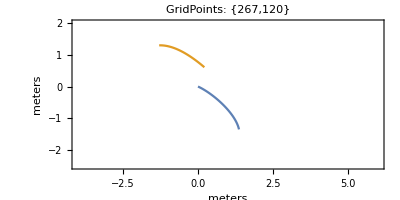

```mathematica
ListLinePlot[state["ObjectsInTunnel"],PlotRange->Evaluate[state["Ranges"]],AspectRatio->Automatic,Axes->False,Frame->True,ImageSize->400,PlotLabel->StringForm["GridPoints: ``",Reverse@state["GridPoints"]],AxesLabel->{"meters","meters"}]
```

### Running the simulation

```mathematica
ProgressIndicator[Dynamic[state["CurrentTime"]],{0,10}]
AbsoluteTiming[WindTunnelIterate[state,10]]
```

{149.415,Null}

### Visualizing the vorticity

Vorticity describes the local rotation of a fluid within it's flow. Higher vorticity represents a lower air-pressure and a lower vorticity represents a higher air-pressure.

Calculate the vorticity for each grid point:

```mathematica
{usol,vsol}={"U","V"}/. state[state["CurrentTime"]];
vort=D[usol[x,y],y]-D[vsol[x,y],x];
```

Assign colors to different vorticity values:

```mathematica
cc=N@Range[-15,15,30/60];
cc=DeleteCases[cc,x_/;-0.1<=x<=0.1];
cname="VisibleSpectrum";
cdata=ColorData[cname];
crange=ColorData[cname,"Range"];
cMinMax={Min[cc],Max[cc]};
colors=cdata[Rescale[#,cMinMax,crange]]&/@cc;
```

Darker red colors represent a higher vorticity while darker purple colors represent lower vorticity.

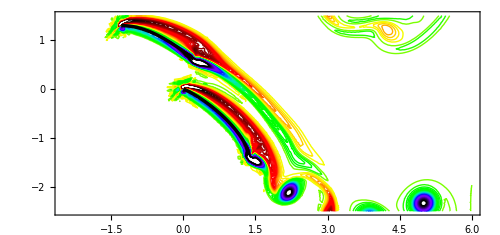

```mathematica
Show[ContourPlot[vort,{x,-2.5,6},{y,-2.5,1.5},AspectRatio->Automatic,ImageSize->500,Contours->cc,ContourShading->None,ContourStyle->colors,PlotRange->{{-2.5,6},{-2.5,1.5},All}],ListLinePlot[state["ObjectsInTunnel"],AspectRatio->Automatic,Axes->False,Frame->True,PlotStyle->Directive[Black,Thickness[0.005]]]]
```

### Visualizing the pressure differences

The first graph is the pressure on the jib and the second is the pressure on the main. The lower lines represent the pressure on the windward side (side the wind is directly hitting) and the upper lines represent the pressure on the leeward side (side the wind is past).

jCp represents the pressure coefficient on different points of the jib.

Plot the pressure on the jib:

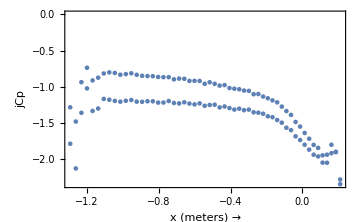

```mathematica
jobjs=Join[Reverse[state["ObjectsInTunnel"][[2]]],Map[Plus[#,{0,0.01}]&,state["ObjectsInTunnel"][[2]]]];
jpsol="P"/. state[state["CurrentTime"]];
jpp=Apply[jpsol,jobjs,1];
jpp=(jpp-jpsol[-3.5,0])/(0.5*state["InternalVelocity"]^2);
ListPlot[Transpose[{jobjs[[All,1]],jpp}],PlotRange->All,Axes->False,Frame->True,FrameLabel->{"x (meters) →","jCp"},FrameStyle->Directive[Black,14],ImageSize->Medium]
```

mCp represents the pressure coefficients on different points of the mainsail.

Plot the pressure on the mainsail:

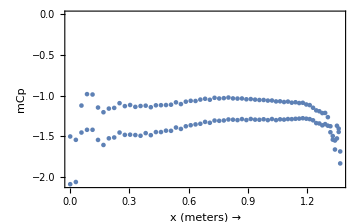

```mathematica
objs=Join[Reverse[state["ObjectsInTunnel"][[1]]],Map[Plus[#,{0,0.01}]&,state["ObjectsInTunnel"][[1]]]];
psol="P"/. state[state["CurrentTime"]];
pp=Apply[psol,objs,1];
pp=(pp-psol[-3.5,0])/(0.5*state["InternalVelocity"]^2);
ListPlot[Transpose[{objs[[All,1]],pp}],PlotRange->All,Axes->False,Frame->True,FrameLabel->{"x (meters) →","mCp"},FrameStyle->Directive[Black,14],ImageSize->Medium]
```

Lift coefficient is the difference between the pressure above and below a body and is used in the lift formula to determine how effective a body is at generating lift.

In order to calculate the lift coefficient for each sail, I take the difference in the pressure coefficient between the windward and leeward side at the center of effort for each sail (the point where the air pressure is the most concentrated):

```mathematica
jCl=Subtract[Drop[#,1]&/@GatherBy[Transpose[{jobjs[[All,1]],jpp}],First][[40]][[1]][[2]],Drop[#,1]&/@GatherBy[Transpose[{jobjs[[All,1]],jpp}],First][[40]][[2]][[2]]]
Cl=Subtract[Drop[#,1]&/@GatherBy[Transpose[{objs[[All,1]],pp}],First][[40]][[1]][[2]],Drop[#,1]&/@GatherBy[Transpose[{objs[[All,1]],pp}],First][[40]][[2]][[2]]]
```

0.340914

0.307188

After calculating the lift coefficient for each sail, I plug the number into the lift formula to calculate the total lift generated by each sail.

The total surface area of the jib and the main are 3.737945986 and 8.6730190131 respectively.

The density I used is the total number of grid points, (267*120)/(10*4.5)=712.

I added the jib lift and main lift to get the total lift generated.

-Graphics-

Calculating the total lift:

```mathematica
jL=jCl*3.7379459869*0.5*712*((wind/0.0008658008658)/1.94384)^2;
mL=Cl*8.6730190131*0.5*712*((wind/0.0008658008658)/1.94384)^2;
L=mL+jL;
{wind/0.0008658008658,-bAngle,L}
```

{23100.,-40,1.98012×10^11}

## Getting my data

### Run a simulation for every combination of wind strength, boat angle, and sail angle

Put all the code into one function:

```mathematica
Mag[s_,b_,w_]:=Module[{sAngle=s,bAngle=b,wind=w*0.0008658008658,rey=(w*0.5144*0.001)/(1.5111*10^(-5))},
state=WindTunnelInitialize[{rey,1,0.5},Function[{x,y},{0,0}],{x,-4,6},{y,-2.5,2},t,"CharacteristicLatticePoints"->20,"CharacteristicLatticeVelocity"->wind,"TunnelBoundaryConditions"->{"Left"->Function[{x,y,t},{1,0}],"Right"->"Outflow","Top"->"Periodic"},"ObjectsInTunnel"->{ParametricRegion[{0.01{Cos[(-bAngle+sAngle)Degree],-Sin[(-bAngle+sAngle)Degree]},0.01*{Sin[(-bAngle+sAngle)Degree],Cos[(-bAngle+sAngle)Degree]}}.{3((1−t)^2)t*50+3(1−t)(t^2)150+(t^3)*194,3((1−t)^2)t*20+3(1−t)(t^2)*30},{{t,0,1}}],ParametricRegion[{0.01{Cos[(-bAngle+sAngle+10)Degree],-Sin[(-bAngle+sAngle+10)Degree]},0.01*{Sin[(-bAngle+sAngle+10)Degree],Cos[(-bAngle+sAngle+10)Degree]}}.{2(1−jt)jt*50+(jt^2)*163,2(1−jt)jt*37.5+(jt^2)*30}+{-Cos[(bAngle)Degree]*(183*0.01),Sin[(bAngle)Degree]*(183*0.01)},{{jt,0,1}}]}];

WindTunnelIterate[state,10];

jobjs=Join[Reverse[state["ObjectsInTunnel"][[2]]],Drop[Map[Plus[#,{0,0.01}]&,state["ObjectsInTunnel"][[2]]],1]];
jpsol="P"/. state[state["CurrentTime"]];
jpp=Apply[jpsol,jobjs,1];
jpp=(jpp-jpsol[-3.5,0])/(0.5*state["InternalVelocity"]^2);
jCl=Subtract[Drop[#,1]&/@GatherBy[Transpose[{jobjs[[All,1]],jpp}],First][[40]][[1]][[2]],Drop[#,1]&/@GatherBy[Transpose[{jobjs[[All,1]],jpp}],First][[40]][[2]][[2]]];

objs=Join[Reverse[state["ObjectsInTunnel"][[1]]],Drop[Map[Plus[#,{0,0.01}]&,state["ObjectsInTunnel"][[1]]],1]];
psol="P"/. state[state["CurrentTime"]];
pp=Apply[psol,objs,1];
pp=(pp-psol[-3.5,0])/(0.5*state["InternalVelocity"]^2);
Cl=Subtract[Drop[#,1]&/@GatherBy[Transpose[{objs[[All,1]],pp}],First][[40]][[1]][[2]],Drop[#,1]&/@GatherBy[Transpose[{objs[[All,1]],pp}],First][[40]][[2]][[2]]];

jL=jCl*3.7379459869*0.5*712*(w/1.94384)^2;
mL=Cl*8.6730190131*0.5*712*(w/1.94384)^2;
L=mL+jL;
{w,sAngle,bAngle,L}
]
```

Import the package for all the kernels:

```mathematica
ParallelEvaluate[CloudImport["https://www.wolframcloud.com/obj/4766c821-ad5b-4a55-9603-9afdf4494e89"]]
```

This function took a lot of time to evaluate so I do not recommend running it. I have already provided the data below in the initialization cell:

```mathematica
allCalc=ParallelMap[Mag@@#&,Tuples[{Range[0,15,2.5],Range[37.5,52.5,2.5],Range[5,20]}]];
```

```mathematica
allCalc = CloudGet[CloudObject[["https://www.wolframcloud.com/obj/ethankong0209/LiftCalculationData.nb"](https://www.wolframcloud.com/obj/ethankong0209/LiftCalculationData.nb)]];
```

### Cleaning the data

Since the sail angle only affects the speed of the boat, I picked the sail angles with the highest lift for each combination of wind strength and boat angle:

```mathematica
liftCalcs=Last/@Partition[SortBy[allCalc,{#[[1]],#[[3]],#[[4]]}&],7];
```

In each list, the first element is the wind strength, the second is the sail angle, the third is the boat angle and the last is the total lift generated.

```mathematica
liftCalcs
```

{{5,0.,-52.5,12031.3},{5,0.,-50.,11129.5},{5,0.,-47.5,10462.4},{5,0.,-45.,9340.7},{5,0.,-42.5,8479.94},{5,0.,-40.,8070.49},{5,0.,-37.5,7690.91},{6,0.,-52.5,17162.2},{6,0.,-50.,15840.8},{6,0.,-47.5,14875.9},{6,0.,-45.,13326.4},{6,0.,-42.5,12136.6},{6,0.,-40.,11556.},{6,0.,-37.5,10986.6},{7,0.,-52.5,23401.8},{7,0.,-50.,21509.6},{7,0.,-47.5,20156.2},{7,0.,-45.,18067.8},{7,0.,-42.5,16450.1},{7,0.,-40.,15640.2},{7,0.,-37.5,14855.9},{8,0.,-52.5,31109.4},{8,0.,-50.,28270.4},{8,0.,-47.5,26284.6},{8,0.,-45.,23448.3},{8,0.,-42.5,21268.9},{8,0.,-40.,20169.1},{8,0.,-37.5,19125.2},{9,0.,-52.5,39846.5},{9,0.,-50.,35989.1},{9,0.,-47.5,33349.1},{9,0.,-45.,29711.4},{9,0.,-42.5,26931.7},{9,0.,-40.,25541.9},{9,0.,-37.5,24216.6},{10,0.,-52.5,49639.5},{10,0.,-50.,44517.2},{10,0.,-47.5,41011.},{10,0.,-45.,36445.4},{10,2.5,-42.5,33056.6},{10,0.,-40.,31398.8},{10,0.,-37.5,29725.7},{11,0.,-52.5,61171.2},{11,0.,-50.,54488.8},{11,0.,-47.5,49925.2},{11,0.,-45.,44347.8},{11,2.5,-42.5,40881.9},{11,0.,-40.,38670.1},{11,0.,-37.5,36768.9},{12,0.,-52.5,73011.7},{12,0.,-50.,64410.5},{12,0.,-47.5,58818.2},{12,0.,-45.,52388.4},{12,2.5,-42.5,49076.5},{12,0.,-40.,46826.},{12,0.,-37.5,44951.7},{13,0.,-52.5,87897.3},{13,0.,-50.,76656.1},{13,0.,-47.5,69262.4},{13,0.,-45.,61417.6},{13,2.5,-42.5,57313.},{13,0.,-40.,55434.},{13,0.,-37.5,53175.9},{14,0.,-52.5,103769.},{14,0.,-50.,90294.6},{14,0.,-47.5,81518.3},{14,0.,-45.,72610.6},{14,2.5,-42.5,68211.6},{14,0.,-40.,66569.1},{14,0.,-37.5,63384.4},{15,0.,-52.5,122107.},{15,0.,-50.,105593.},{15,0.,-47.5,94531.9},{15,0.,-45.,83796.8},{15,0.,-42.5,78133.2},{15,0.,-40.,76585.1},{15,0.,-37.5,71821.6},{16,0.,-52.5,141331.},{16,0.,-50.,122169.},{16,0.,-47.5,108838.},{16,0.,-45.,95833.9},{16,0.,-42.5,89222.8},{16,0.,-40.,86768.9},{16,0.,-37.5,80731.1},{17,0.,-52.5,163972.},{17,0.,-50.,141997.},{17,0.,-47.5,126153.},{17,0.,-45.,110687.},{17,0.,-42.5,102952.},{17,0.,-40.,99210.6},{17,0.,-37.5,90954.},{18,0.,-52.5,184522.},{18,0.,-50.,160730.},{18,0.,-47.5,142999.},{18,0.,-45.,124960.},{18,0.,-42.5,115956.},{18,0.,-40.,110351.},{18,0.,-37.5,100106.},{19,0.,-52.5,203456.},{19,0.,-50.,179002.},{19,0.,-47.5,160248.},{19,0.,-45.,139945.},{19,0.,-42.5,129431.},{19,0.,-40.,122221.},{19,0.,-37.5,109978.},{20,0.,-52.5,232600.},{20,0.,-50.,207188.},{20,0.,-47.5,186096.},{20,0.,-45.,161270.},{20,0.,-42.5,146233.},{20,0.,-40.,134972.},{20,0.,-37.5,119316.}}

## Setting Up the Environment

Plot the wind vector field to simulate a real life scenario of the wind:

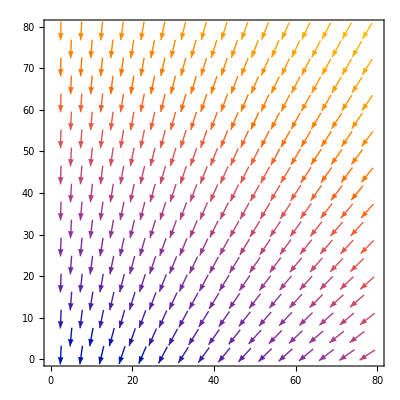

```mathematica
VectorPlot[{-x,-(y+50)},{x,0,80},{y,0,80}]
```

Make a reset function to reset the environment:

```mathematica
sailReset[]:=Module[{},
windx=-x;
windy=-(y+50);
onStarboard=RandomChoice[{1,2}];
currentPos={20,5};
goal={60,80};
timeTaken=0;
score=0;]
```

Now I can use sailReset[]

```mathematica
sailReset[]
```

## Optimizing the Path

### Brute force

The brute force method is extremely simple yet effective. It requires a high number of iterations of random moves and then picks the best option. In general, brute force can be accurate as long as the number of iterations is high but it is also computationally expensive.

Check all possible moves at each position based on the wind strength:

```mathematica
possibleMoves[x_,y_]:=Module[{xpos=x,ypos=y},
Cases[liftCalcs,{Round[Sqrt[(-xpos)^2+(-(ypos+50))^2]/7.],___,___,___}]
]
```

Function to move the boat in the selected direction and count the time taken to make that move:

```mathematica
move[x_,y_,bA_]:=Module[{windSpeed=Round[Sqrt[(-x)^2+(-(y+50))^2]/7],windAngle=ArcTan[(-(y+50)),(-x)],boatAngle=bA,liftMag},
liftMag=(Flatten[Cases[liftCalcs,{windSpeed,___,-boatAngle,___}]][[4]]);
{currentPos=Flatten[{If[Divisible[onStarboard,2],{currentPos[[1]]-=(Cos[windAngle+(180+boatAngle)Degree])*5,currentPos[[2]]+=(Sin[windAngle+(180+boatAngle)Degree])*5},{currentPos[[1]]+=(Cos[windAngle+(180-boatAngle)Degree])*5,currentPos[[2]]+=(Sin[windAngle+(180-boatAngle)Degree])*5}]}],distanceFromGoal=Sqrt[(goal[[1]]-currentPos[[1]])^2+(goal[[2]]-currentPos[[2]])^2];
score+=1000/Sqrt[liftMag]}
]
```

Select from the eight possible moves, seven different boat angles and tacking (going in the opposite direction by turning approximately ninety degrees into the direction of the wind):

```mathematica
chooseMove[x_,y_,m_Integer]:=Module[{choice},
If[m<8,choice=possibleMoves[x,y][[m]];{move[x,y,-choice[[3]]],choice[[3]]},onStarboard+=1;timeTaken+=5;"Tack"]
]
```

Randomly choosing a move while preventing the boat from exiting the environment:

```mathematica
randomMove[x_,y_]:=Module[{choice},
If[x<1||y<1||x>85||y>85,onStarboard+=1;timeTaken+=5;chooseMove[currentPos[[1]],currentPos[[2]],RandomChoice[Range[1,8]]];"Tack",
chooseMove[currentPos[[1]],currentPos[[2]],RandomChoice[Range[1,8]]]]
]
```

Makes the boat randomly move thirty times and counts the final score of the thirty moves (the final distance from the goal plus the total time taken to make those thirty moves plus five times the amount of times it tacks):

```mathematica
sailReset[];
{Table[randomMove[currentPos[[1]],currentPos[[2]]],30],score+=(timeTaken+distanceFromGoal);score}
sailReset[];
```

{{{{{18.4951,9.76814},5.66962},-52.5},{{{16.3578,14.2883},11.1456},-47.5},{{{13.9932,18.6939},16.6215},-47.5},{{{10.8816,22.6077},22.2649},-40.},{{{7.57002,26.3538},27.9083},-40.},{{{4.93243,30.6015},31.9516},-52.5},Tack,{{{8.21284,26.8281},35.6524},-52.5},{{{12.363,24.0395},40.7377},-40.},{{{16.5554,21.3148},45.6835},-42.5},Tack,{{{13.7283,25.4388},51.1836},-42.5},{{{10.3706,29.1437},56.3986},-37.5},{{{7.50026,33.2377},60.8741},-47.5},{{{4.46677,37.2124},64.9974},-47.5},Tack,{{{8.32112,34.0274},69.5114},-42.5},{{{11.8969,30.5325},73.4517},-50.},{{{15.4877,27.0532},77.1525},-52.5},{{{19.3934,23.9314},81.4365},-50.},Tack,{{{17.4557,28.5407},85.4797},-52.5},{{{15.345,33.0733},89.5229},-52.5},{{{11.9971,36.787},94.2395},-37.5},{{{8.97902,40.7734},98.2746},-45.},{{{5.98035,44.7744},102.074},-47.5},Tack,{{{10.0054,41.808},105.95},-40.},{{{13.9031,38.6764},109.985},-45.},Tack},201.893}

This list above shows the path taken. The first item shows the current position and the total time taken to make all the previous moves. The second item shows the angle the boat sailed to get to its current position.

Repeat the above function 100,000 times:

```mathematica
all=Table[sailReset[];{Table[randomMove[currentPos[[1]],currentPos[[2]]],30],score+=(timeTaken+distanceFromGoal);score},100000];
```

By having a lower score, it means the path taken takes a less amount of time, is closer to the final goal, and makes less tacks.

Choose the path with the lowest score:

```mathematica
bruteBest=SortBy[all,#[[-1]]&][[1]]
plotBruteBest=Flatten[Drop[#,-1]&/@Insert[First/@DeleteCases[Flatten[Drop[bruteBest,-1],1],"Tack"],{{20.,5.},0},1],1];
```

{{{{{24.698,3.28851},7.04137},-40.},Tack,{{{23.6044,8.16746},12.711},-52.5},Tack,{{{28.362,6.62963},18.9681},-40.},{{{33.2719,5.68443},25.3941},-37.5},{{{38.169,4.6755},31.4877},-42.5},{{{42.9968,3.37458},36.2272},-50.},{{{47.9958,3.27456},41.8706},-40.},{{{52.9474,2.58009},46.6102},-50.},{{{57.9473,2.59749},51.3588},-45.},{{{62.9303,2.18525},55.402},-52.5},{{{67.8837,2.86665},59.916},-42.5},Tack,{{{68.9308,7.75576},63.8562},-50.},{{{70.0165,12.6365},67.2292},-52.5},{{{69.8581,17.634},71.4765},-40.},{{{70.157,22.625},74.9789},-47.5},{{{69.6352,27.5977},78.8548},-40.},{{{70.0191,32.5829},81.7165},-52.5},{{{69.3919,37.5434},85.294},-42.5},{{{69.2525,42.5415},88.155},-50.},{{{68.1115,47.4096},91.3299},-40.},{{{67.8901,52.4047},93.7994},-52.5},{{{67.3278,57.373},96.2937},-50.},{{{66.6397,62.3254},98.788},-50.},{{{65.8299,67.2594},101.152},-50.},{{{64.689,72.1275},103.65},-47.5},{{{63.856,77.0576},105.723},-52.5},{{{62.7043,81.9231},107.92},-50.}},126.238}

Find the total time taken:

```mathematica
bruteTime=bruteBest[[1]][[-1]][[1]][[-1]]+5*Count[Flatten[bruteBest,1],"Tack"]
```

122.92

Visualize the path taken:

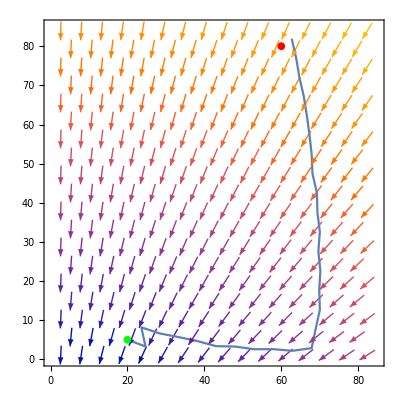

```mathematica
Show[VectorPlot[{windx,windy},{x,0,85},{y,0,85}],ListLinePlot[plotBruteBest,Frame->True,PlotRange->{{0,85},{0,85}}],Graphics[{Directive[Green,EdgeForm[None]],Disk[{20,5},1]}],Graphics[{Directive[Red,EdgeForm[None]],Disk[{60,80},1]}]
]
```

### Greedy Algorithm

The greedy algorithm is another optimization method. It works by evaluating all the possible options in a local area and choosing the option with the lowest score. It is called the greedy method because it often chooses the immediate, short term gains and misses out on the options that require small sacrifices which may lead to long term benefits.

New function that is independent from the previous that does not randomize the tack the boat is on:

```mathematica
greedySailReset[]:=Module[{},
windx=-x;
windy=-(y+50);
onStarboard=1;
currentPos={20,5};
goal={60,80};
timeTaken=0;
score=0;]
```

```mathematica
greedySailReset[]
```

Define a way to reset a test position without changing the boat's actual position:

```mathematica
greedyReset[]:=Module[{},
greedyPos={currentPos[[1]],currentPos[[2]]};
greeyScore=0;
greedyTime=0;
]
```

```mathematica
greedyReset[]
```

Determine the theoretical distance from goal after making a move:

```mathematica
greedyMove[x_,y_,bA_]:=Module[{windSpeed=Round[Sqrt[(-x)^2+(-(y+50))^2]/7],windAngle=ArcTan[(-(y+50)),(-x)],boatAngle=bA,liftMag},
liftMag=(Flatten[Cases[liftCalcs,{windSpeed,___,-boatAngle,___}]][[4]]);
{greedyPos=Flatten[{If[Divisible[onStarboard,2],{greedyPos[[1]]-=(Cos[windAngle+(180+boatAngle)Degree])*5,greedyPos[[2]]+=(Sin[windAngle+(180+boatAngle)Degree])*5},{greedyPos[[1]]+=(Cos[windAngle+(180-boatAngle)Degree])*5,greedyPos[[2]]+=(Sin[windAngle+(180-boatAngle)Degree])*5}]}],distanceFromGoal=Sqrt[(goal[[1]]-greedyPos[[1]])^2+(goal[[2]]-greedyPos[[2]])^2];
greedyTime=1000/Sqrt[liftMag],greedyScore=distanceFromGoal}
]
```

List the position, time taken, and distance from goal for each possible move:

```mathematica
evalAllMoves[x_,y_]:=Module[{choices,count=0},Reap[{onStarboard+=1;
Map[(count+=1;
greedyReset[];
Sow[Append[greedyMove[x,y,-#],count]])&,#[[3]]&/@possibleMoves[x,y]],onStarboard+=1;
Map[(count+=1;
greedyReset[];
Sow[Append[greedyMove[x,y,-#],count]])&,#[[3]]&/@possibleMoves[x,y]],onStarboard+=1;}][[2,1]]]
```

Choose the move which has the lowest distance from the goal:

```mathematica
greedyChooseMove[x_,y_,m_Integer]:=Module[{choice},
If[m<8,choice=possibleMoves[x,y][[m]];{move[x,y,-choice[[3]]],choice[[3]]},timeTaken+=5;onStarboard+=1;choice=possibleMoves[x,y][[m-7]];{move[x,y,-choice[[3]]],choice[[3]]}]
]
```

Evaluate the best move until the goal is reached:

```mathematica
greedyPath=Table[best=SortBy[evalAllMoves[currentPos[[1]],currentPos[[2]]],#[[-2]]&][[1]];greedyChooseMove[currentPos[[1]],currentPos[[2]],best[[4]]],42]
```

{{{{18.4951,9.76814},5.66962},-52.5},{{{16.7599,14.4574},10.6792},-52.5},{{{14.8123,19.0625},15.1676},-52.5},{{{12.6681,23.5794},19.6559},-52.5},{{{10.3414,28.0051},23.6992},-52.5},{{{7.84535,32.3375},27.7424},-52.5},{{{12.0829,29.6836},32.4589},-37.5},{{{9.66825,34.0619},36.1598},-52.5},{{{13.9568,31.4913},40.8764},-37.5},{{{11.6263,35.9149},44.5773},-52.5},{{{15.9654,33.4306},49.2938},-37.5},{{{13.7214,37.8987},52.9947},-52.5},{{{18.1102,35.5032},57.3312},-37.5},{{{15.9544,40.0146},61.0321},-52.5},{{{20.3915,37.7098},65.3686},-37.5},{{{18.3251,42.2627},68.7416},-52.5},{{{22.8088,40.05},73.0781},-37.5},{{{20.8321,44.6427},76.4511},-52.5},{{{25.3605,42.5228},80.4231},-37.5},{{{23.4736,47.1531},83.5274},-52.5},{{{28.0443,45.126},87.4994},-37.5},{{{26.2464,49.7916},90.6037},-52.5},{{{30.8569,47.8569},94.3352},-37.5},{{{29.1469,52.5554},97.1969},-52.5},{{{33.7947,50.712},100.928},-37.5},{{{32.171,55.441},103.79},-52.5},{{{36.8533,53.6873},107.31},-37.5},{{{35.3138,58.4444},109.97},-52.5},{{{40.0281,56.7784},113.489},-37.5},{{{38.5703,61.5612},116.149},-52.5},{{{43.3139,59.9806},119.465},-37.5},{{{41.9354,64.7869},121.934},-52.5},{{{46.7058,63.2891},125.25},-37.5},{{{45.4037,68.1165},127.578},-52.5},{{{50.1985,66.6987},130.739},-37.5},{{{48.9698,71.5454},133.067},-52.5},{{{53.7867,70.2045},136.082},-37.5},{{{52.6285,75.0685},138.299},-52.5},{{{57.4653,73.8015},141.315},-37.5},{{{56.3746,78.6811},143.532},-52.5},{{{61.2294,77.4849},146.427},-37.5},{{{58.9714,81.946},149.322},-37.5}}

Clean the list so it can be plotted:

```mathematica
plotGreedypath=Insert[#[[1]][[1]]&/@greedyPath,{20,5},1];
```

Find the total time taken:

```mathematica
greedyTotalTime=timeTaken+greedyPath[[-1]][[1]][[2]]
```

174.322

Visualize the path:

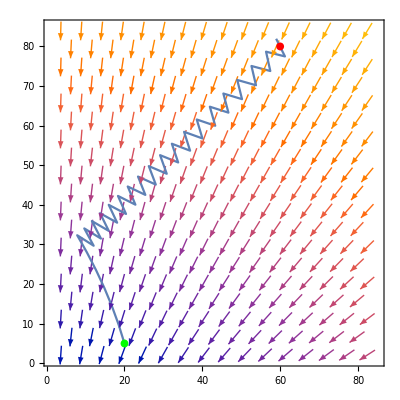

```mathematica
Show[VectorPlot[{windx,windy},{x,1,85},{y,1,85}],ListLinePlot[plotGreedypath,Frame->True,PlotRange->{{1,85},{1,85}}],Graphics[{Directive[Green,EdgeForm[None]],Disk[{20,5},1]}],Graphics[{Directive[Red,EdgeForm[None]],Disk[{60,80},1]}]
]
```

## Analysis

Graph the methods versus time taken:

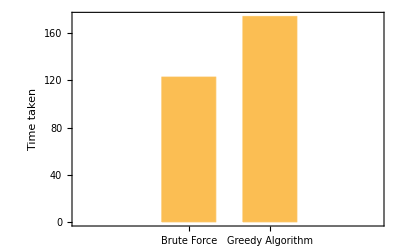

```mathematica
BarChart[{bruteTime,greedyTotalTime},ChartLabels->{"Brute Force","Greedy Algorithm"},Frame->True,FrameLabel->{{"Time taken",""},{"","Algorithm vs time"}},BarSpacing->Large]
```

Plot the two paths side by side:

```mathematica
{Show[VectorPlot[{windx,windy},{x,0,85},{y,0,85}],ListLinePlot[plotBruteBest,Frame->True,PlotRange->{{0,85},{0,85}}],Graphics[{Directive[Green,EdgeForm[None]],Disk[{20,5},1]}],Graphics[{Directive[Red,EdgeForm[None]],Disk[{60,80},1]}]
],Show[VectorPlot[{windx,windy},{x,1,85},{y,1,85}],ListLinePlot[plotGreedypath,Frame->True,PlotRange->{{1,85},{1,85}}],Graphics[{Directive[Green,EdgeForm[None]],Disk[{20,5},1]}],Graphics[{Directive[Red,EdgeForm[None]],Disk[{60,80},1]}]
]}
```

{-Graphics-,-Graphics-}

Looking at the paths the different methods take, it may seem that the greedy algorithm takes a more direct path towards the goal, however it still has a higher time taken compared to the brute force method as each tack has a punishment of 5 seconds.  Looking at the wind vector field by itself, I would expect the optimal path to be somewhere on the right as the wind shifts to the right as x increases, therefore lifting the boat angle higher up and decreasing the total distance required to sail. Sailing towards the right side of the course and taking the lift is exactly what the brute force method decided to do.

Graph the boat angle at each move:

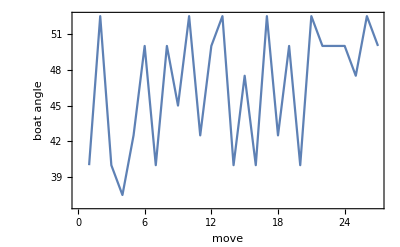

```mathematica
ListLinePlot[-#[[-1]]&/@(DeleteCases[bruteBest[[1]],"Tack"]),Frame->True,FrameLabel->{{"boat angle",""},{"move","Move vs Boat Angle"}}]
```

Find the mean, median, and mode boat angle:

```mathematica
Mean[-#[[-1]]&/@(DeleteCases[bruteBest[[1]],"Tack"])]
Median[-#[[-1]]&/@(DeleteCases[bruteBest[[1]],"Tack"])]
Commonest[-#[[-1]]&/@(DeleteCases[bruteBest[[1]],"Tack"])]
```

46.6667

50.

{50.}

Looking at the plot and the mean median mode values, the boat tends to oscillate between speed and distance up until the last ten moves where it decides to sail at a lower angle to get to the final destination faster. Oscillating between speed and distance is exactly what happens in a typical race where the general strategy is to go for speed and then use that speed to sail a higher angle for a short period and repeat.

## Limitations

I did not have exact measurements for my sail dimensions and I eyeballed the sail-shape and angles for both sails. This may result in wind flowing incorrectly past the sails, affecting the final lift calculations. For example, for almost all the combinations of wind-strength and boat-angles, having a sail angle of zero degrees was optimal, which in theory should not be true; a larger sail angle should be more optimal for lower boat angles.

I assumed the sails to be rigid and for current to be nonexistent, which makes the sailboat generate more lift and move faster than theoretically possible.

I used quite a low lattice velocity and very few grid points in my wind tunnel simulations to save on computational time, this may result in less accurate movement of air particles affecting lift calculations.

The wind vector plot is not an accurate representation of wind in real life, with the wind shifts being too controlled and dramatic in angles as well as the wind gradually increasing by a large margin as the boat advanced through the course.

I limited the boat from sailing below x or y equals one which likely caused the boat to sail a slightly less efficient path. In the brute force method, it sailed on starboard for one move before tacking off towards the left although starting on port and sailing straight to the lay-line(imaginary line where you would tack and be able to reach the goal/mark) may have been faster.

## Conclusion

Although the simulations and optimization algorithms aren't perfect, this project gave some interesting insights into how my sailboat works and confirmed how different sail headings can affect the lift on the sails. An application I could use for this could be after a day of racing I could import the wind vector data for the day and compare the route I sailed to the optimal route as determined by my algorithms.

### Further work

In the future, there are quite a few improvements I would like to make:

Make the sail measurements fully accurate and implement a third variable called vang which flattens the mainsail.

Introduce downwind by adding the third and largest sail of the boat, the kite.

Introduce a grid search algorithm to find the optimal path.

Use real wind vector data instead of self-made vector fields.

## Acknowledgements

I want to thank my mentor Daniele for his support as well as teaching assistants Karan, Nicolo, and Sophie.

## References

Kantor, Ilya. “Bezier Curve.” The Modern JavaScript Tutorial, 30 Nov. 2022, javascript.info/bezier-curve. 

Mokhasi, Paritosh. “Building a Lattice Boltzmann–Based Wind Tunnel with the Wolfram Language-Wolfram Blog.” Wolfram Blog RSS, 7 Nov. 2019, blog.wolfram.com/2019/11/07/building-a-lattice-boltzmann-based-wind-tunnel-with-the-wolfram-language/. 

“Sail Balance.” DIY Wood Boat, www.diy-wood-boat.com/sail-balance.html. Accessed 13 July 2023.